## Two kings and a white rook

```mathematica
n=3;(*size of the board*)
(*position = {{white king x, white king y}, {black king x, black king y}, {rook x ({-1,-1} if the rook was taken), rook y} 1->white's move; 0->black's move}*)
```

```mathematica
flipVertically[{{w1_,w2_},{b1_,b2_},{-1,-1},m_}]:={{n+1-w1,w2},{n+1-b1,b2},{-1,-1},m};
flipVertically[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_}]:={{n+1-w1,w2},{n+1-b1,b2},{n+1-r1,r2},m};
flipHorizontally[{{w1_,w2_},{b1_,b2_},{-1,-1},m_}]:={{w1,n+1-w2},{b1,n+1-b2},{-1,-1},m};
flipHorizontally[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_}]:={{w1,n+1-w2},{b1,n+1-b2},{r1,n+1-r2},m};
flipDiagonally[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_}]:={{w2,w1},{b2,b1},{r2,r1},m};
toStandardPosition[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_}]:=Module[{ans={{w1,w2},{b1,b2},{r1,r2},m}},
If[w1>Ceiling[n/2],ans=flipVertically[ans]];
If[ans[[1,2]]>Ceiling[n/2],ans=flipHorizontally[ans]];
If[ans[[1,1]]>ans[[1,2]],ans=flipDiagonally[ans]];
ans
];
```

```mathematica
kingMoves[x_,y_]:=Module[{ans={}},
If[x>1,
AppendTo[ans,{x-1,y}];
If[y>1,AppendTo[ans,{x-1,y-1}]];
If[y<n,AppendTo[ans,{x-1,y+1}]];
];
If[x<n,
AppendTo[ans,{x+1,y}];
If[y>1,AppendTo[ans,{x+1,y-1}]];
If[y<n,AppendTo[ans,{x+1,y+1}]];
];
If[y>1,AppendTo[ans,{x,y-1}]];
If[y<n,AppendTo[ans,{x,y+1}]];
ans
];(*returns a list of valid moves for a single king*)
```

```mathematica
rookMoves[x_,y_]:=If[x==-1,{},DeleteCases[Join[{#,y}&/@Range[n],{x,#}&/@Range[n]],{x,y}]];(*returns a list of valid moves for a single rook*)
```

```mathematica
validPosition[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_}]:=(!(Abs[w1-b1]<=1&&Abs[w2-b2]<=1))&&(((!(w1==r1&&w2==r2))&&(!(b1==r1&&b2==r2))&&(!(m==1&&(r1==b1&&(w1!=b1||w2<Min[b2,r2]||w2>Max[b2,r2]))))&&(!(m==1&&(r2==b2&&(w2!=b2||w1<Min[b1,r1]||w1>Max[b1,r1])))))||r1==-1);
```

```mathematica
nextPositions[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_}]:=Module[{ans={}},
If[m==1,(*white's move*)
ans=Join[{#,{b1,b2},{r1,r2},0}&/@kingMoves[w1,w2],{{w1,w2},{b1,b2},#,0}&/@rookMoves[r1,r2]]
];
If[m==0,(*black's move*)
ans={{w1,w2},#,{r1,r2},1}&/@kingMoves[b1,b2];
ans=ans/.{{a_,b_},{c_,d_},{c_,d_},1}->{{a,b},{c,d},{-1,-1},1}
];
ans=DeleteCases[ans,p_/; validPosition[p]==False];
DeleteDuplicates[toStandardPosition/@ans]
];
```

```mathematica
ChessPosition[{{1,2},{3,1},{1,3},1}]
```

♚ |   |  
  |   |  
  | ♔ | ♖

```mathematica
ChessPosition/@nextPositions[{{1,2},{3,1},{1,3},1}]
```

{  |   | ♚
  |   |  
♖ | ♔ |  ,♚ |   |  
  |   |  
♔ |   | ♖,♚ |   |  
  |   | ♖
  | ♔ |  ,♚ |   | ♖
  |   |  
  | ♔ |  ,♚ |   |  
  |   |  
♖ | ♔ |  }

```mathematica
edgesFromPosition[p_]:={p->#}&/@nextPositions[p];
```

```mathematica
positions=DeleteDuplicates[toStandardPosition/@DeleteCases[Join[
Flatten[Table[{{w1,w2},{b1,b2},{r1,r2},m},{w1,n},{w2,n},{b1,n},{b2,n},{r1,n},{r2,n},{m,0,1}],6],
Flatten[Table[{{w1,w2},{b1,b2},{-1,-1},m},{w1,n},{w2,n},{b1,n},{b2,n},{m,0,1}],4]
],
p_/; validPosition[p]==False
]];(*all possible positions*)
```

```mathematica
edges=Flatten[edgesFromPosition/@positions,2];
```

```mathematica
MakeBoxes[position:ChessPosition[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_}],form:StandardForm]:=Module[{table=Table[" ",{i,n},{j,n}],grid},
table[[n-w1+1,w2]]=♔;
table[[n-b1+1,b2]]=♚;
If[r1!=-1,table[[n-r1+1,r2]]=♖];
grid=Grid[table,Dividers->All,ItemSize->{1.,1.},
Background -> {Automatic,Automatic,Flatten[Table[{i, j} -> If[EvenQ[i+j],LightGray, White], {i, n}, {j, n}]]}];
ToBoxes@Interpretation[grid,position]
]
```

```mathematica
ChessPositionData[ChessPosition[data_]]:=data;
```

```mathematica
labels=#->Placed[ChessPosition[#],Tooltip]&/@positions;
```

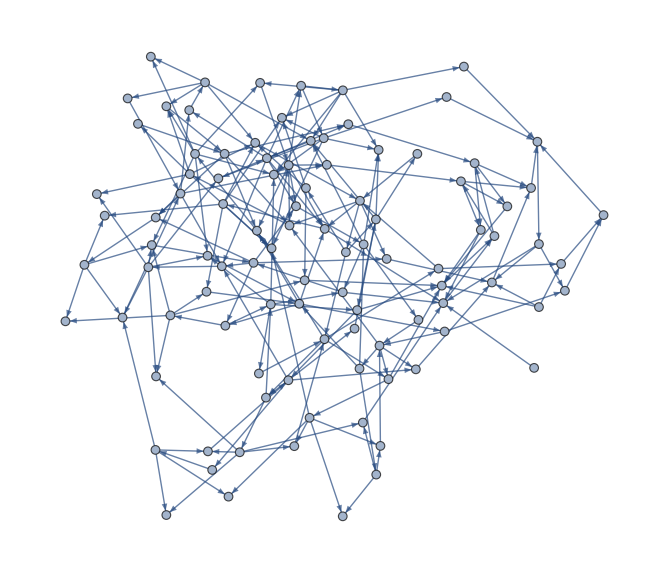

```mathematica
graph=Graph[edges,VertexLabels->labels]
```